# The Lotka - Volterra system

## Define the LV system

First we define the symbols for functions of time and parameters used in the model. We will make all definitions valid for arbitrary dimension.

```mathematica
n=2;    (* dimensionality of the system *)
```

```mathematica
coordSymb=Subscript[x,#]&/@Range[n];       (* generates coordinate symbols *)
coord=coordSymb⟦#⟧[t]&/@Range[n];              (* generates coordinate functions of time *)
parametersS=Table[Subscript[r,ToString[i]],{i,1,n}];               (* generates scaling parameters symbols *)
parametersA=Table[If[i==j,0,Subscript[a,ToString[i]<>ToString[j]]],{i,1,n},{j,1,n}];       (* generates interaction parameters symbols *)
allParameters=DeleteCases[Flatten[Prepend[parametersA,parametersS]],0];         (* the list of all parameters *)
```

```mathematica
Print["Species are designated by = ", coordSymb, " and by ", coord, " as functions of time."]
Print["Scaling parameters = ", parametersS]
Print["Interaction matrix without self-interaction = ", parametersA]
Print["All parameters = ", allParameters]
```

Species are designated by = {x_1,x_2} and by {x_1[t],x_2[t]} as functions of time.

Scaling parameters = {r_1,r_2}

Interaction matrix without self-interaction = {{0,a_12},{a_21,0}}

All parameters = {r_1,r_2,a_12,a_21}

Define the vector field corresponding to the system of differential equations

```mathematica
fVector=Table[
coord⟦i⟧parametersS⟦i⟧+Sum[coord⟦i⟧parametersA⟦i,j⟧coord⟦j⟧,
{j,1,n}],{i,1,n}
];
LVSystem=Thread[D[coord,t]==fVector]
Print["The vector field in the species space = ", MatrixForm[fVector]]
Print["And the equations of the dynamical system = ", MatrixForm[LVSystem]]
```

{x_1'[t]==r_1 x_1[t]+a_12 x_1[t] x_2[t],x_2'[t]==r_2 x_2[t]+a_21 x_1[t] x_2[t]}

The vector field in the species space = (r_1 x_1[t]+a_12 x_1[t] x_2[t]
r_2 x_2[t]+a_21 x_1[t] x_2[t])

And the equations of the dynamical system = (x_1'[t]==r_1 x_1[t]+a_12 x_1[t] x_2[t]
x_2'[t]==r_2 x_2[t]+a_21 x_1[t] x_2[t])

stable points - ADD LATER

## Define the numerical solver and plotter

It is useful to define a function that gives the Rule for implementing the chosen parameters into any expression

```mathematica
ChooseParameters[modelParameters_]:=Thread[Flatten[allParameters]->Flatten[modelParameters]]    (* use this to give values to the parameters *)
```

The following function numerically solves the system of equations, provided the system, initial conditions, parameters and the duration of simulation

```mathematica
LVSolution[coord_,system_,modelParameters_,initcond_,tEnd_]:=NDSolve[
Join[system,initcond]/.ChooseParameters[modelParameters],
coord,
{t,0,tEnd}
];
```

The following are the function for plotting the solution, and a helping function that displays the parameters in the text form, used in options of Plot.

```mathematica
DisplayParameters[allParameters_,modelParameters_]:=TextString[Row[Table[ToString[allParameters⟦i⟧//TraditionalForm]<>"="<>ToString[modelParameters⟦i⟧]<>"  ",{i,1,Length[allParameters]}]]]
```

```mathematica
plt[params_,solution_,tend_,plottitle_]:=Plot[
Evaluate[solution⟦1,All,1⟧/.solution],
{t,0,tend},
AxesOrigin->{0,0},(* RegionFunction->Function[{x,y},tail<x<tail+4] *)PlotLegends->Table[ToString[solution⟦1,i,1⟧,TraditionalForm],{i,1,n}],PlotLabel->plottitle<>DisplayParameters[allParameters,params]]
```

## Numerical and visual analysis of the Lotka-Volterra system

### Numerically solve the system for a given choice of parameters and initial conditions

Let us choose some values of parameters (they all need to be positive since we require this system to describe realistic predator-prey population dynamics) and choose the initial conditions; we can always come back here to change them in order to explore the model

```mathematica
modelParameters={1.5,-3.,-1.,1.};
initialConditions=Thread[(coord/.t->0)=={12,5}]     (* give initial conditions here *)
tend=30;      (* time period over which to run the simulation *)
ChooseParameters[modelParameters]
```

{x_1[0]==12,x_2[0]==5}

{r_1→1.5,r_2→-3.,a_12→-1.,a_21→1.}

Numerically solve the system using previously defined function LVSolution

```mathematica
sol=LVSolution[coord,LVSystem,modelParameters,initialConditions,tend];
```

Plot the time evolution of the two populations

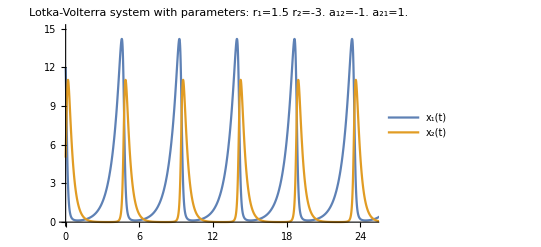

```mathematica
Show[plt[modelParameters,sol,tend,"Lotka-Volterra system with parameters: \n"],
PlotRange->{{0,25},{0,15}}]
```

### Numerically find dependence of the system on two varied parameters

For the next example let's choose to vary the two scaling parameters and fix the interaction parameters. We interactively then change the parameters to display its influence on the trajectory in the state space

```mathematica
pfun=ParametricNDSolveValue[
Join[LVSystem,initialConditions]/.ChooseParameters[{a,c,-1.,1.}],coordSymb,{t,0,25},{a,c}];
```

```mathematica
Manipulate[
ParametricPlot[Evaluate@{pfun[a,c]⟦1⟧[t],pfun[a,c]⟦2⟧[t]},{t,0,25},PlotRange->{{0,20},{0,20}},ImageSize->500,AxesLabel->Table[ToString[sol⟦1,i,1⟧,TraditionalForm],{i,1,n}],PlotLabel->"State space trajectory"],
{a,0.2,1.5,0.1},{c,-2.0,2.0,0.1}]
```

Seems like the trajectory is always closed. This is the limit cycle of the Lotka-Volterra system.

### 3D plot of both coordinates against time

We can also plot the state space at each moment in time (used as the third dimension), like a sequence of snapshots.  ADD LABELS

```mathematica
Manipulate[
ParametricPlot3D[
Evaluate@{pfun[a,c]⟦1⟧[t],pfun[a,c]⟦2⟧[t],t},
{t,0,25},
PlotRange->{{-1,a+15},{-1,c+30},{0,25}},
ImageSize->600,
Boxed->False
],
{a,0.2,20,0.2},
{c,-2.0,0.,0.2}
]
```

### Plot the vector field and vary the parameters

We can get insight into the system’s behavior without solving the differential equations. Simply examine the flow of the vector field in the state space. We do this interactively, leaving all four parameters arbitrary.  STABLE POINT - ADD LATER

```mathematica
Manipulate[
StreamDensityPlot[fVector/.Thread[coord->{x,y}]/.ChooseParameters[{a,-c,-b,d}],{x,0,20},{y,0,20},ColorFunction->"BeachColors",ImageSize->600,PlotLabel->"2D Lotka-Volterra vector field with parameters: \n"<>DisplayParameters[allParameters,{a,-c,-b,d}]],
{a,0.1,2.,0.1},
{c,0.01,2.,0.1},
{b,0.01,2.,0.1},
{d,0.01,2.,0.1}
]
```